#### INSTRUCTIONS: Run common_funs.nb, ES_FindSymGroups.nb, chooseTmat.nb, then this notebook

#### Choose Tmat, then check

```mathematica
Tmat=TmatMar17;
```

```mathematica
Tmat=TmatBrown;
```

```mathematica
Tmat=TmatIgel;
```

```mathematica
Tmat==Transpose[Tmat]
MatrixNote[Tmat]
PrintVoigt[Tmat]
```

## The superlattice

```mathematica
WantDetails="WantDetails";
```

#### Do NOT change these. (But you might want to change RangeΣ below.)

```mathematica
RangeSigmaAll={TRIV,MONO,ORTH,TET,CUBE,ISO,XISO,TRIG};
```

#### Closest Tmat for each Sigma symmetry class

```mathematica
OutputFor[Tmat,#]&/@RangeSigmaAll;
```

#### Be sure the Nodes all have decimal points. No integers. That is, 4., not 4, and 2., not 2

```mathematica
ww=1;ww=1.2;
Clear[SigmaOfPt];
SigmaOfPt[{x_,y_}]:="";
Node[ISO]:={0.,5-.5};  SigmaOfPt[Node[ISO]]="ISO";
Node[XISO]:={-1ww,4.};SigmaOfPt[Node[XISO]]="XISO";
Node[TRIG]:={-1ww,2.5};SigmaOfPt[Node[TRIG]]="TRIG";
Node[CUBE]:={   1ww,4.};SigmaOfPt[Node[CUBE]]="CUBE";
Node[TET]:={  1ww,3.};SigmaOfPt[Node[TET]]="TET";
Node[ORTH]:={  1ww,2.};SigmaOfPt[Node[ORTH]]="ORTH";
Node[MONO]:={0.,1+.5};SigmaOfPt[Node[MONO]]="MONO";
Node[TRIV]:={0.,0+.5};SigmaOfPt[Node[TRIV]]="TRIV";
dummy;
```

```mathematica
SigmaOfN[n_,path_]:=SigmaOfPt[points[[path[[n]]]]]
```

```mathematica
LatticeBlank:={Arrowheads[.0008],Thickness[.0015],Dashing[{.013,.013}],
{Arrow[{Node[TRIV],Node[MONO]},.25]},  (* from TRIV to MONO *)
{Arrow[{Node[MONO],Node[ORTH]},.25]},  (* from MONO to ORTH *)
{Arrow[{Node[ORTH],Node[TET]},.2]},   (* from ORTH *)
{Arrow[{Node[TET],Node[CUBE]},.2]},   (* from TET to CUBE *)
{Arrow[{Node[TRIG],Node[XISO]},.2]},   (* from TRIG to XISO *)
{Arrow[{Node[TET],Node[XISO]},.3]},   (* from TET to XISO *)
{Arrow[{Node[TRIG],Node[CUBE]},.3]},   (* from TRIG to CUBE *)
{Arrow[{Node[MONO],Node[TRIG]},.3]},   (* from MONO to TRIG *)
{Arrow[{Node[CUBE],Node[ISO]},.25]},   (* from CUBE to ISO *)
{Arrow[{Node[XISO],Node[ISO]},.25]}  (* from XISO to ISO *)
};
```

#### This definition will change if we want the winding path.

```mathematica
SmatOfPt[Node[TRIV]]=Tmat;
SmatOfPt[Node[MONO]]=Closest[Tmat,MONO];
SmatOfPt[Node[ORTH]]=Closest[Tmat,ORTH];
SmatOfPt[Node[TET]]  =Closest[Tmat,TET];
SmatOfPt[Node[XISO]]=Closest[Tmat,XISO];
SmatOfPt[Node[ISO]]  =Closest[Tmat,ISO];
SmatOfPt[Node[TRIG]]=Closest[Tmat,TRIG];SmatOfPt[Node[CUBE]]=Closest[Tmat,CUBE];
```

#### Specify the discretization increment between symmetry classes The path indices will depend on dt and can be found from the lattice diagram below.

```mathematica
dt=0.5;
(* TRIV to ISO *)
PathXISO={6,7,8,12,14,15,16,10,3,5,11}; 
PathCUBE={6,7,8,12,14,15,16,17,18,13,11}; 
(* ISO to TRIV *)
PathXISO={11,5,3,10,16,15,14,12,8,7,6}; 
PathCUBE={11,13,18,17,16,15,14,12,8,7,6};
```

```mathematica
dt=0.2;
PathXISO={25,17,13,9,8,6,12,16,29,33,43,42,41,40,39,38,36,32,30,26,24,23,22,21,20,19}; 
PathCUBE={25,28,31,35,37,48,47,46,45,44,43,42,41,40,39,38,36,32,30,26,24,23,22,21,20,19};
```

#### Defining the points and the elastic maps at each point. t=0 represents the higher-symmetry end of the segment t=1 represents the lower-symmetry end of the segment

```mathematica
PointsAndSmat:=Union[ Flatten[Table[{
{t Node[TRIV]+(1-t) Node[MONO],t SmatOfPt[Node[TRIV]]+(1-t) SmatOfPt[Node[MONO]]},
{t Node[MONO]+(1-t) Node[ORTH],t SmatOfPt[Node[MONO]]+(1-t) SmatOfPt[Node[ORTH]]},
{t Node[ORTH]+(1-t)Node[TET],  t SmatOfPt[Node[ORTH]]+(1-t) SmatOfPt[Node[TET]]},
{t Node[TET]  +(1-t)Node[XISO],t SmatOfPt[Node[TET]]  +(1-t) SmatOfPt[Node[XISO]]},
{t Node[TET]  +(1-t) Node[CUBE],t SmatOfPt[Node[TET]]  +(1-t) SmatOfPt[Node[CUBE]]},
{t Node[XISO]+(1-t) Node[ISO],  t SmatOfPt[Node[XISO]]+(1-t) SmatOfPt[Node[ISO]]},
{t Node[MONO]+(1-t) Node[TRIG],t SmatOfPt[Node[MONO]]+(1-t) SmatOfPt[Node[TRIG]]},
{t Node[TRIG]+(1-t) Node[XISO],t SmatOfPt[Node[TRIG]]+(1-t) SmatOfPt[Node[XISO]]},
{t Node[TRIG]+(1-t) Node[CUBE],t SmatOfPt[Node[TRIG]]+(1-t) SmatOfPt[Node[CUBE]]},
{t Node[CUBE]+(1-t) Node[ISO],  t SmatOfPt[Node[CUBE]]+(1-t) SmatOfPt[Node[ISO]]}},{t,0,1,dt}],1]];
points=#[[1]]&/@PointsAndSmat;
Length[points]
```

#### Here are the points and their positions in the list. (If the crossing points are superimposed, you can perturb SigmaOfPt above.)

```mathematica
points
Graphics[{LatticeBlank,PointSize[.03],
Point/@points,
Text[Style[Position[points,#],12],#+{.3,0}]&/@points},ImageSize->200]
```

#### Save. This finishes the definition of SmatOfPt

```mathematica
(SmatOfPt[#[[1]]]=#[[2]])&/@PointsAndSmat;  (* SAVE *)
```

#### Example: Point 3 in the lattice (closest XISO for dt = 0.5)

```mathematica
points[[3]]
MatrixForm[SmatOfPt[points[[3]]]]
```

#### Example: the initial Tmat

```mathematica
MatrixForm[Tmat]
MatrixForm[SmatOfPt[points[[6]]]]
```

#### Example: point 8 (closest MONO for dt=0.5)

```mathematica
MatrixForm[Closest[Tmat,MONO]]
MatrixForm[SmatOfPt[points[[8]]]]
```

#### Example: all matrices in a path

#### One Tmat on the XISO path

```mathematica
MatrixForm[SmatOfPt[points[[PathXISO[[5]]]]]]
```

#### Display the set of Tmats as BB and as Voigt (for a chosen path)

```mathematica
(
Print["point ",#," (", Length[PathXISO]," total)"];
PrintVoigt[SmatOfPt[points[[#]]]];Print["betaTRIV = ",Round[MakeReal[AngleMatrix[SmatOfPt[Node[TRIV]],SmatOfPt[points[[#]]]]/Degree],0.01]];
Print["betaMONO = ",Round[MakeReal[AngleMatrix[SmatOfPt[Node[MONO]],SmatOfPt[points[[#]]]]/Degree],0.01]];
Print["betaISO = ",Round[MakeReal[AngleMatrix[SmatOfPt[Node[ISO]],SmatOfPt[points[[#]]]]/Degree],0.01]];
Print["------------------------------------------------------------"];
)&/@PathXISO
```

## Beta and lattice preliminaries

#### Any 999s in the 8 - tuples/Degree mean you have not run all OutputFor

```mathematica
βT[Tmat_,Σ_]:=999Degree;   (* This should have been entered in FindSymGroupsForPublic *)
βofPt[{x_,y_},Sigma_]:=βT[SmatOfPt[{x,y}],Sigma];
Beta8tuple[pt_]:=βofPt[pt,#]&/@RangeSigmaAll;
```

```mathematica
RangeSigmaAll
```

```mathematica
Beta8tuple[points[[5]]]/Degree
```

#### check: closest-MONO point should have betaMONO = 0

```mathematica
βofPt[points[[8]],MONO]/Degree
```

#### Again, any 999s in the 8-tuples/Degree mean you have not run all OutputFor. When you run the lattice for the first time you will see lots of 999s.

```mathematica
pickpoint=12;
Graphics[{LatticeBlank,PointSize[.015],
Point/@points,
{Red,
Arrow[{points[[pickpoint]],Node[#]},.1]&/@RangeSigmaAll},
If[True,Text[Style[Round[Beta8tuple[#]/Degree,.01],13],#,{-1.15,0}]&/@points]},ImageSize->900]
Graphics[{LatticeBlank,PointSize[.03],
Point/@points,
Text[Style[Position[points,#],12],#+{.3,0}]&/@points},ImageSize->200]
```

## Beta curves

#### Examples

```mathematica
points[[6]]
```

```mathematica
PathXISO[[4]]
```

```mathematica
points[[PathXISO[[4]]]]
```

```mathematica
Table[{n,βofPt[points[[PathXISO[[n]]]],ORTH]/Degree},{n,1,Length[PathXISO]}]
```

#### Preliminaries for the main diagram.

```mathematica
BetaPts[Sigma_,PathX_]:={Point/@Table[{n,βofPt[points[[PathX[[n]]]],Sigma]/Degree},{n,1,Length[PathX]}],
                                                            Line[Table[{n,βofPt[points[[PathX[[n]]]],Sigma]/Degree},{n,1,Length[PathX]}]]};
```

```mathematica
hue[MONO]=Black;   BetaText[MONO]="β_MONO";
hue[ORTH]=Purple; BetaText[ORTH]="β_ORTH";
hue[TET]  =Blue;      BetaText[TET]  ="β_TET";
hue[CUBE]=Orange; BetaText[CUBE]="β_CUBE";
hue[XISO]=Green;   BetaText[XISO]="β_XISO";
hue[ISO]  =Red;        BetaText[ISO]   ="β_ISO";
hue[TRIG]=Cyan;     BetaText[TRIG] ="β_TRIG";
dummy;
```

#### Specify the beta curves to be plotted (for initial testing, try {ORTH,ISO} )

```mathematica
RangeΣ={MONO};
```

```mathematica
RangeΣ={ORTH,ISO};
```

```mathematica
RangeΣ={MONO,ORTH,TET,CUBE,ISO,XISO,TRIG};
```

#### Determine the scale for the y-value of the custom tick labels on the x-axis

```mathematica
yText[PathX_,RangeΣ_]:=Max[βofPt[points[[PathX[[Length[PathX]]]]],#]&/@RangeΣ]/Degree;
yText[PathXISO,RangeΣ]
```

#### MAIN DIAGRAM This will place a text label like β_XISO^ (15.98) at the far right of the plot

```mathematica
ptsz=0.013;
BetaPtsDiagram[PathX_,RangeΣ_]:=Graphics[{PointSize[ptsz],
{hue[#],BetaPts[#,PathX]}&/@RangeΣ,
Table[Text[Style[PathX[[n]],12],{n,-0.06yText[PathX,RangeΣ]}],{n,1,Length[PathX]}], (* integer tick label (3) *)
Text[Style[SigmaOfN[#,PathX],11],{#,-0.12yText[PathX,RangeΣ]}]&/@Range[Length[PathX]], (* text tick label (XISO) *)
Text[Style[SequenceForm[BetaText[#]," (",Round[βofPt[points[[PathX[[Length[PathX]]]]],#]/Degree,0.01],")"],{hue[#],15}],{1.03Length[PathX],βofPt[points[[PathX[[Length[PathX]]]]],#]/Degree},{-1,0}]&/@RangeΣ},
Axes->True,Ticks->{None,Range[0,50,5]},AxesOrigin->{1,0},TicksStyle->12,AspectRatio->1,ImageSize->500]
```

```mathematica
Round[βofPt[points[[PathXISO[[Length[PathXISO]]]]],XISO]/Degree,0.01]
```

#### OutputAllPts[Sigma] will give the beta values for the specified Sigma and for all the points.

```mathematica
OutputAllPts[Sigma_]:=OutputFor[SmatOfPt[#],Sigma]&/@points;
```

```mathematica
(*OutputAllPts[ORTH]*)
```

```mathematica
(*OutputAllPts[ISO]*)
```

#### Example: NMinimize error message for TmatMar17 (pathological case)

```mathematica
(* Ttest=SmatOfPt[points[[11]]];
MatrixForm[Ttest]
OutputFor[Ttest,ORTH]
DistToVΣofU[Ttest,UsHat[{6.265341668513891,-3.129228992900632,1.5350976895707746}],ORTH] *)
```

#### KEY COMMAND : this will execute OutputAllPts for all specified Sigmas Progress can be tracked by checking which Sigma the calculation is on (see order in RangeΣ)

```mathematica
WantDetails="NoWantDetails";
```

```mathematica
OutputAllPts/@RangeΣ
```

### Show one path for a single symmetry class

```mathematica
BetaPtsDiagram[PathXISO,{XISO}]
```

### Show two paths for a single symmetry class

```mathematica
Show[{
BetaPtsDiagram[PathXISO,{XISO}],
BetaPtsDiagram[PathCUBE,{XISO}]}]
```

### Display all chosen Sigma curves for the path through XISO

```mathematica
BetaPtsDiagram[PathXISO,RangeΣ]
```

### Display all chosen Sigma curves for the path through CUBE

```mathematica
BetaPtsDiagram[PathCUBE,RangeΣ]
```

### Display all chosen Sigma curves for the paths through CUBE and XISO

```mathematica
Show[{
BetaPtsDiagram[PathXISO, RangeΣ],
BetaPtsDiagram[PathCUBE,RangeΣ]}]
```

## For reference: Igel

### Path through XISO (Igel)

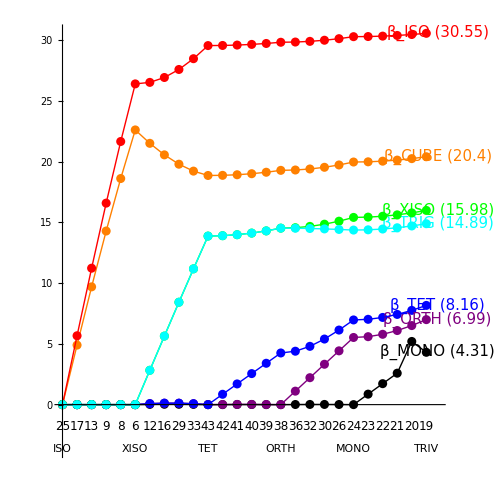

### Path through CUBE (Igel)

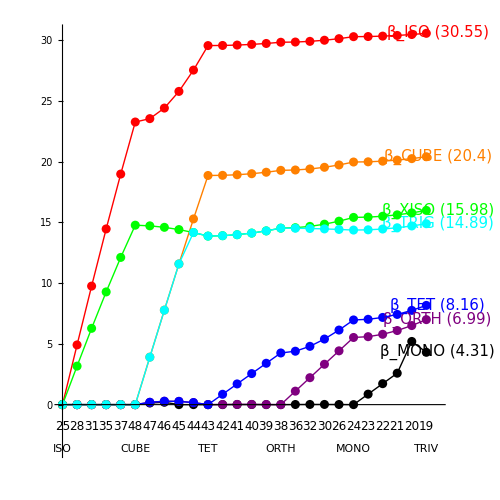

### problematic point between TRIV and MONO (Igel):

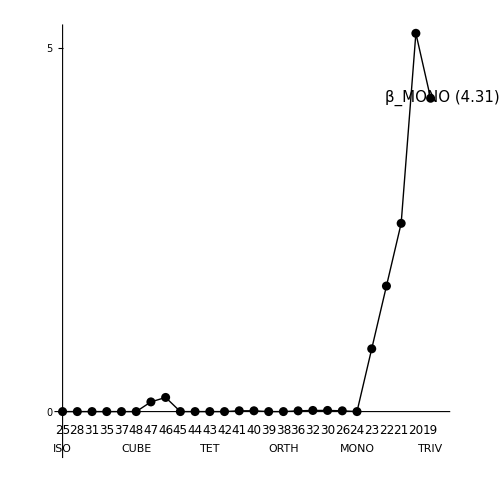

### Paths through XISO and CUBE (Igel)

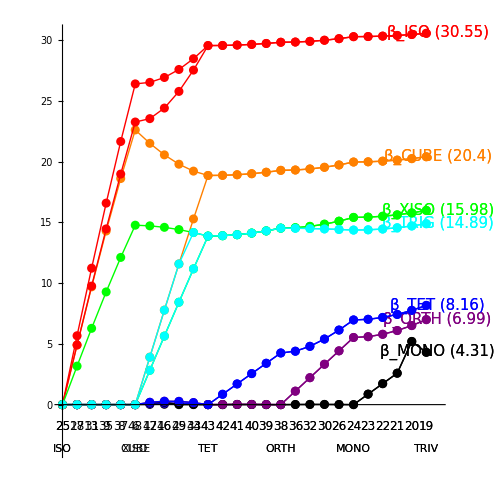

## For reference: Brown

### Path through XISO (Brown)

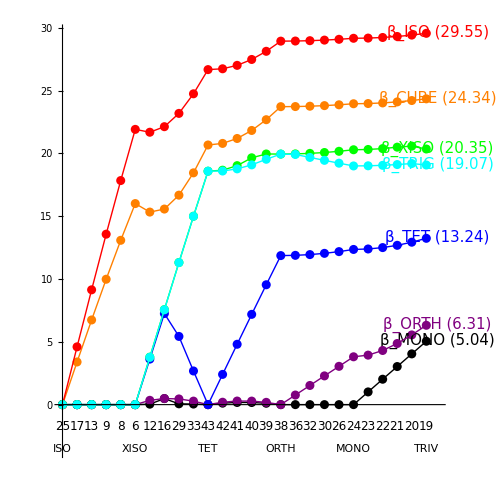

### problematic point between TET and XISO (Brown, dt = 0.2):

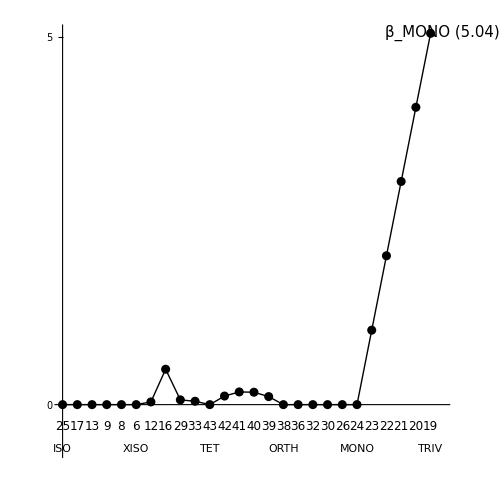

### problematic point at closest MONO (Brown, dt = 0.5):

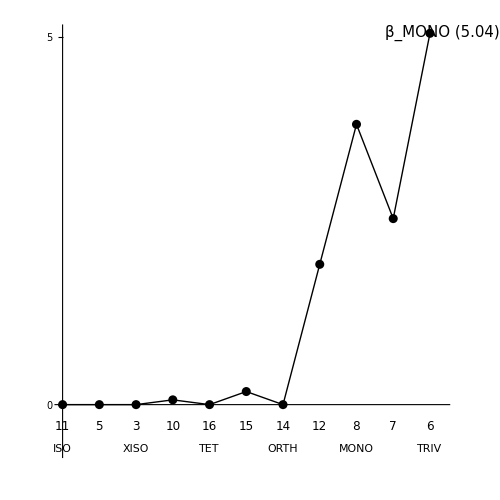

### Path through CUBE (Brown)

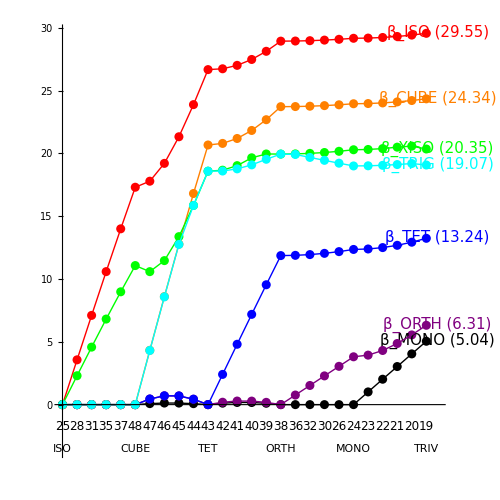

### Paths through XISO and CUBE (Brown)

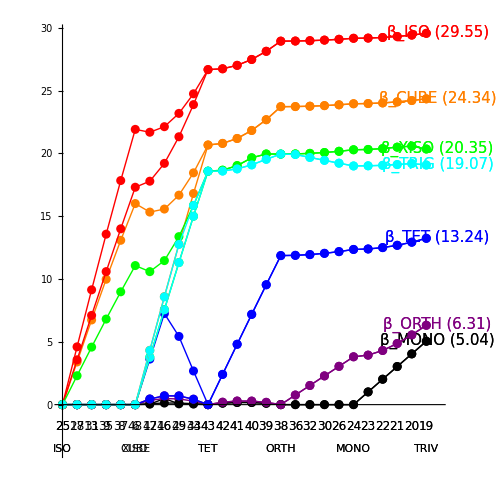

## For reference: TmatMar17

### Path through XISO (TmatMar17)

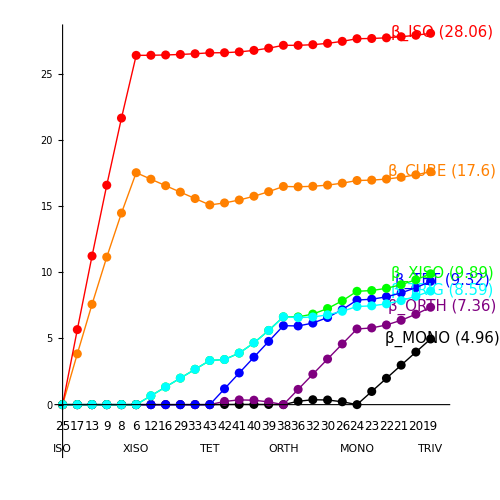

### Path through CUBE (TmatMar17)

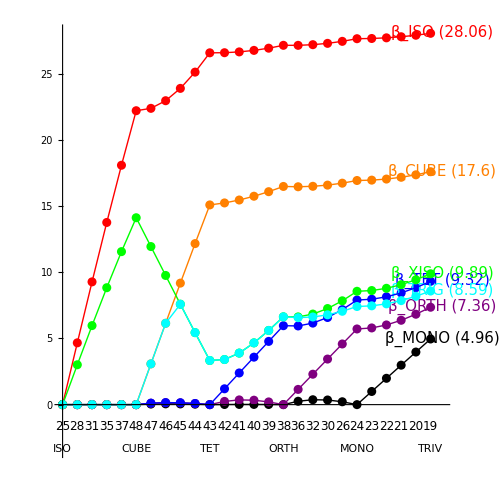

### Paths through XISO and CUBE (TmatMar17)

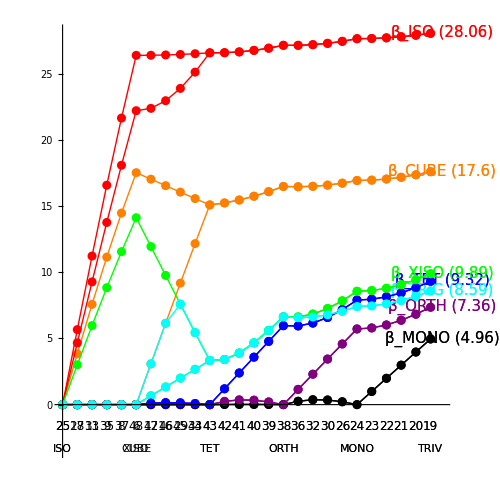

## Super lattices

### Beta angles for Igel (target point is 12, halfway between MONO and ORTH)

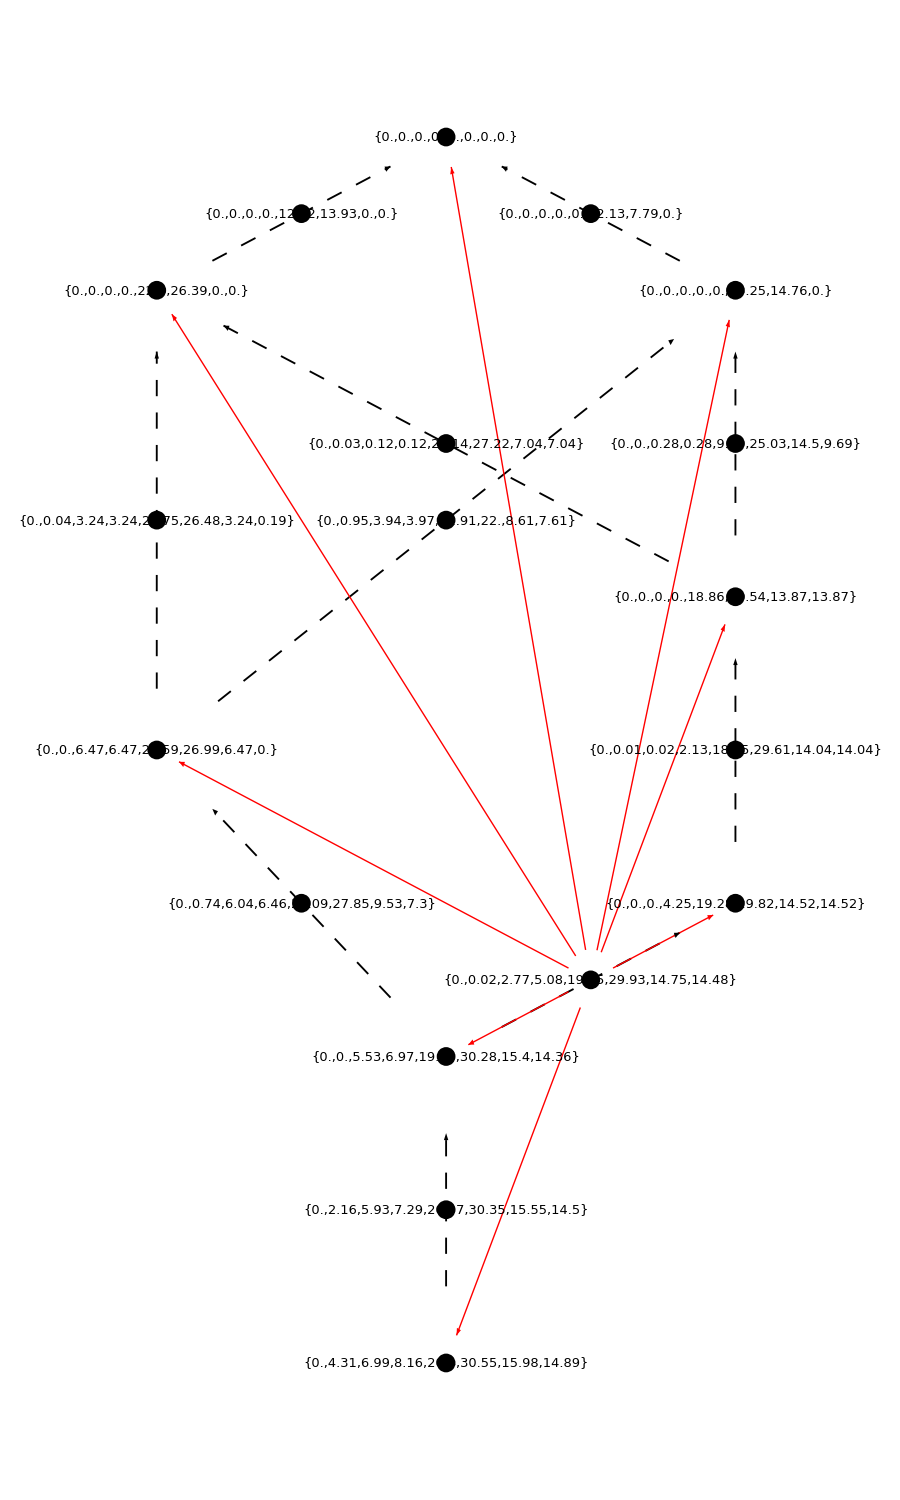

### Beta angles for Brown (target point is 12, halfway between MONO and ORTH)

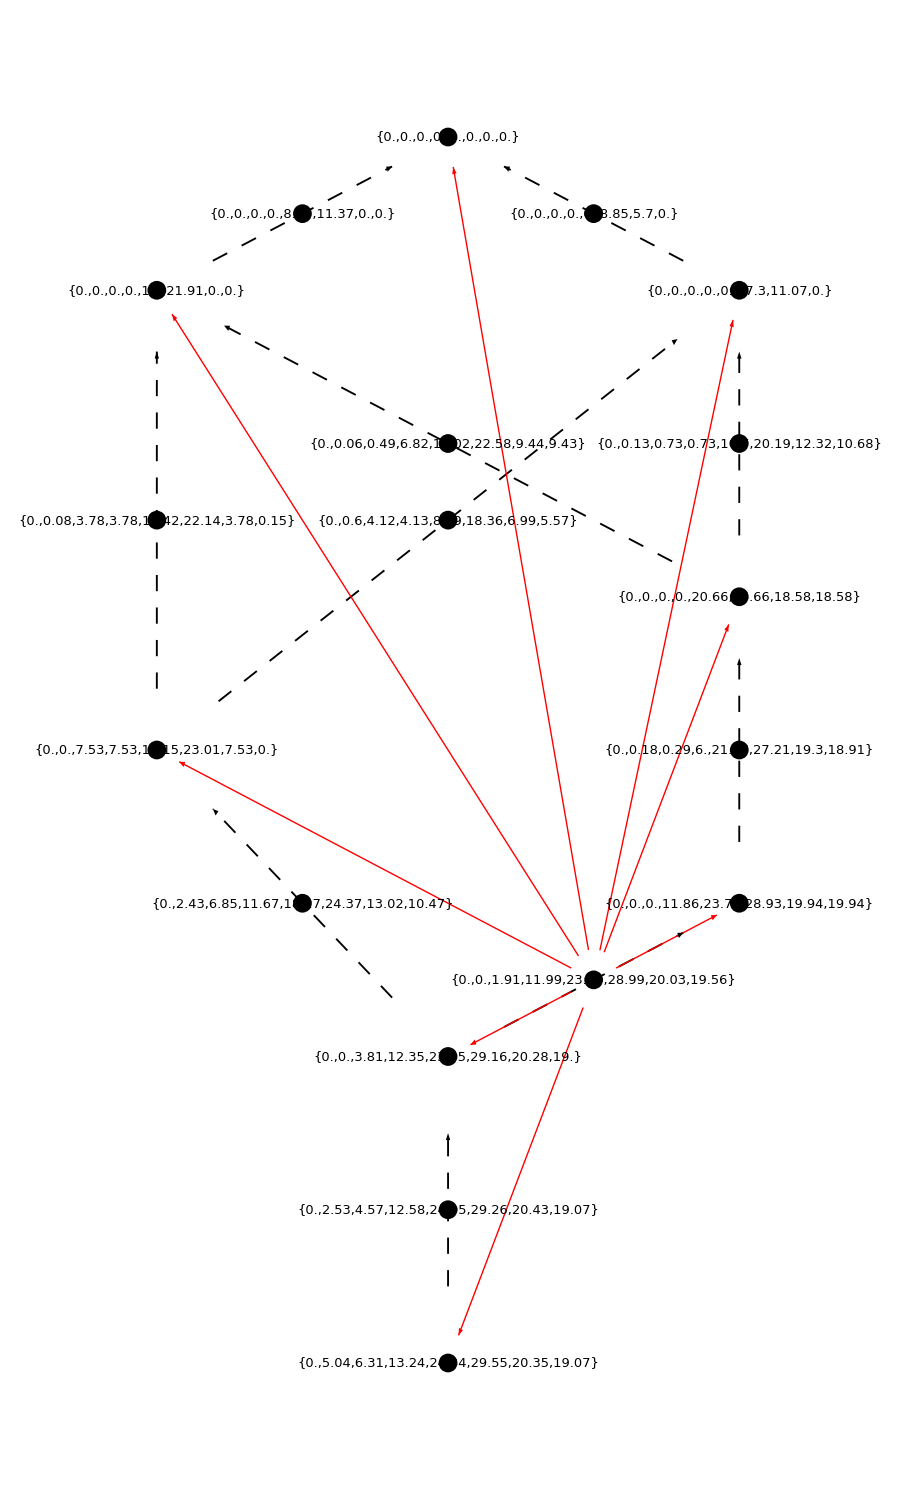

### Beta angles for TmatMar17 (target point is 12, halfway between MONO and ORTH)